```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Elastic Collisions in Lab Frame

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

#### Second solution is physical one

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

```mathematica
etransfer=FullSimplify[Efin/ϵ,Assumptions->{ϵ>0,M>0,m>0}];
```

```mathematica
1/(2Pi)Integrate[etransfer,{θ,0,2Pi},Assumptions->{ϵ>0,M>0,m>0}]//FullSimplify
```

M^2/(m+M)^2

#### Proper calculation (lab frame angle not exactly isotropic, unlike CM angle) yields ζ= (M^2+m^2)/(m+M)^2~M^2/(m+M)^2for heavy nuclei

```mathematica
ζ=M^2/(m+M)^2;
```

```mathematica
dedxelastic=Piecewise[{{ϵ(n/Z σ/10),ϵ≤10},{0,ϵ>10}}];
```

```mathematica
dedxnonelastic=Piecewise[{{ϵ (n/Z σ),ϵ>10},{0,ϵ≤10}}];
```

#### In units of MeV/(10^-5 cm)

```mathematica
Convert[(Mega ElectronVolt)^4 Barn(200 Mega ElectronVolt Fermi)^-2,(Mega ElectronVolt)^2]//N
```

0.0025 ElectronVolt^2 Mega^2

```mathematica
Convert[ElectronVolt^2 Mega^2*(200 Mega ElectronVolt*Fermi)^-1,Mega ElectronVolt/Centimeter]//N
```

(5.×10^10 ElectronVolt Mega)/Centimeter

#### Elastic and Nonelastic stopping powers

```mathematica
nucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,1,10^10},PlotStyle->{Purple,Thick}];
```

```mathematica
meson=LogLogPlot[ReplaceAll[ReplaceAll[dedxnonelastic,{n->8,Z->6}],{σ->0.1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,1,10^10},PlotStyle->{Purple,Thick}];
```

```mathematica
elasticnucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxelastic,{n->8,Z->6}],{σ->1,M->12000,m->1000}](0.0025)(5.*^5),{ϵ,1,10^10},PlotStyle->{Green,Thick}];
```

```mathematica
elasticmeson=elasticnucleon=LogLogPlot[ReplaceAll[ReplaceAll[dedxelastic,{n->8,Z->6}],{σ->1,M->12000,m->140}](0.0025)(5.*^5),{ϵ,1,10^10},PlotStyle->{Green,Thick}];
```

```mathematica
canvasnuclear=LogLogPlot[10^20,{ϵ,1,10^10},Frame->True,PlotRange->{10^-3,10^5},FrameLabel->{"MeV","MeV/(10^-5cm)"},PlotLabel->"Stopping Power"];
```

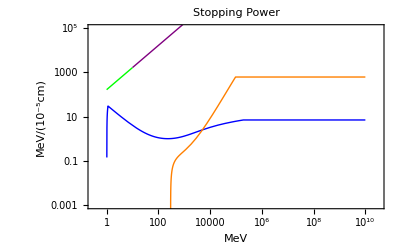

```mathematica
Show[canvasnuclear,proton,protonpauli,elasticnucleon,nucleon]
```

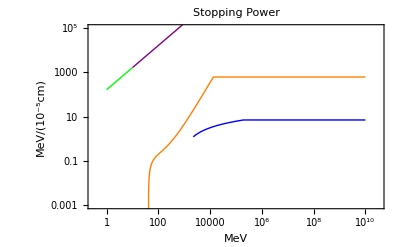

```mathematica
Show[canvasnuclear,pion,pionpauli,elasticmeson,meson]
```

#### Heating Length - $$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$$

#### Shower length

```mathematica
showerlength=Convert[Integrate[ReplaceAll[dedxnonelastic^-1,{α->1/137,M->12000,Z->6,n->8,m->1000,σ->0.1}],{ϵ,10,ϵ},Assumptions->{ϵ>10}] 1/((Mega ElectronVolt)^3 Barn)*(200 Mega ElectronVolt*Fermi)^3,Centimeter];
```

#### Final-state nucleons - elastic scattering

```mathematica
finalnucleon=Convert[Integrate[ReplaceAll[dedxelastic^-1,{α->1/137,M->12000,Z->6,n->8,m->1000,σ->0.1}],{ϵ,1,10}] 1/((Mega ElectronVolt)^3 Barn)*(200 Mega ElectronVolt*Fermi)^3,Centimeter];
```

#### Ion mean free path?

```mathematica
ionmfp=Convert[1/(10^32 Centimeter^-3 1 Barn),Centimeter];
```

```mathematica
hadronL=(showerlength+finalnucleon+ionmfp)1/Centimeter;
```

```mathematica
hadronL//Expand
```

1.2534×10^-6+6.×10^-8 Log[ϵ]

```mathematica
Hadron=LogLogPlot[hadronL,{ϵ,10,10^15},PlotStyle->{Green,Thick}];
```

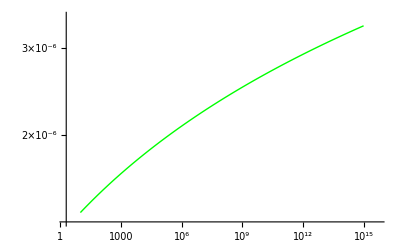

```mathematica
Hadron
```

```mathematica
canvasL=LogLogPlot[10^20,{ϵ,100,10^15},Frame->True,PlotRange->{10^-7,10^-4},FrameLabel->{"Incident Energy (MeV)","Heating Length (cm)"},PlotLabel->"Heating Length for SM Particle Species"];
```

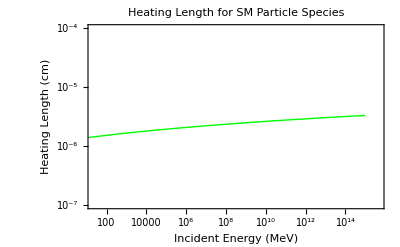

```mathematica
Show[canvasL,Hadron]
```